```mathematica
(* Compute points of intersection of circle0 with projection of circle1 *)
```

```mathematica
p=a00+a10*c+a01*s+a20*c^2+a11*s*c+a02*s^2
```

a00+a10 c+a20 c^2+a01 s+a11 c s+a02 s^2

```mathematica
q=-1+c^2+s^2
```

-1+c^2+s^2

```mathematica
clist=Factor[CoefficientList[Resultant[p,q,s],c]]
```

{(a00-a01+a02) (a00+a01+a02),2 (a00 a10+a02 a10-a01 a11),a01^2-2 a00 a02-2 a02^2+a10^2-a11^2+2 a00 a20+2 a02 a20,-2 (a02 a10-a01 a11-a10 a20),a02^2+a11^2-2 a02 a20+a20^2}

```mathematica
f=Expand[(c0+r1*(c*u0+s*v0))^2+(c1+r1*(c*u1+s*v1))^2-r0^2]
```

c0^2+c1^2-r0^2+2 c c0 r1 u0+c^2 r1^2 u0^2+2 c c1 r1 u1+c^2 r1^2 u1^2+2 c0 r1 s v0+2 c r1^2 s u0 v0+r1^2 s^2 v0^2+2 c1 r1 s v1+2 c r1^2 s u1 v1+r1^2 s^2 v1^2

```mathematica
term0=Factor[Coefficient[f,c^2]]
```

r1^2 (u0^2+u1^2)

```mathematica
term1=Factor[Coefficient[f,s^2]]
```

r1^2 (v0^2+v1^2)

```mathematica
term2=Factor[Coefficient[f,s*c]]
```

2 r1^2 (u0 v0+u1 v1)

```mathematica
g=Simplify[f-term0*c^2-term1*s^2-term2*s*c]
```

c0^2+c1^2-r0^2+2 c0 r1 (c u0+s v0)+2 c1 r1 (c u1+s v1)

```mathematica
term3=Factor[Coefficient[g,c]]
```

2 r1 (c0 u0+c1 u1)

```mathematica
term4=Factor[Coefficient[g,s]]
```

2 r1 (c0 v0+c1 v1)

```mathematica
h=Simplify[g-term3*c-term4*s]
```

c0^2+c1^2-r0^2

```mathematica
Simplify[((a00+a02)-a01)*((a00+a02)+a01)-clist[[1]]]
```

0

```mathematica
Simplify[2*((a00+a02)*a10-a01*a11)-clist[[2]]]
```

0

```mathematica
Simplify[a01^2+a10^2-a11^2+2*(a00+a02)*(a20-a02)-clist[[3]]]
```

0

```mathematica
Simplify[2*(a01*a11+a10*(a20-a02))-clist[[4]]]
```

0

```mathematica
Simplify[a11^2+(a20-a02)^2-clist[[5]]]
```

0

```mathematica
(* projection of circle1 onto plane of circle0, ellipse equation *)
```

```mathematica
A={{u0,v0},{u1,v1}}
```

{{u0,v0},{u1,v1}}

```mathematica
diff={x0-c0,x1-c1}
```

{-c0+x0,-c1+x1}

```mathematica
B=Simplify[Transpose[Inverse[A]].Inverse[A]]
```

{{(u1^2+v1^2)/(u1 v0-u0 v1)^2,-(u0 u1+v0 v1)/(u1 v0-u0 v1)^2},{-(u0 u1+v0 v1)/(u1 v0-u0 v1)^2,(u0^2+v0^2)/(u1 v0-u0 v1)^2}}

```mathematica
Simplify[Det[B*Det[A]^2]]
```

(u1 v0-u0 v1)^2

```mathematica
mat=Simplify[B*Det[A]^2]
```

{{u1^2+v1^2,-u0 u1-v0 v1},{-u0 u1-v0 v1,u0^2+v0^2}}

```mathematica
Factor[Det[mat]]
```

(u1 v0-u0 v1)^2

```mathematica
Eigensystem[mat]
```

{{1/2 (u0^2+u1^2+v0^2+v1^2-√((-u0^2-u1^2-v0^2-v1^2)^2-4 (u1^2 v0^2-2 u0 u1 v0 v1+u0^2 v1^2))),1/2 (u0^2+u1^2+v0^2+v1^2+√((-u0^2-u1^2-v0^2-v1^2)^2-4 (u1^2 v0^2-2 u0 u1 v0 v1+u0^2 v1^2)))},{{-(-u0^2+u1^2-v0^2+v1^2-√(u0^4+2 u0^2 u1^2+u1^4+2 u0^2 v0^2-2 u1^2 v0^2+v0^4+8 u0 u1 v0 v1-2 u0^2 v1^2+2 u1^2 v1^2+2 v0^2 v1^2+v1^4))/(2 (u0 u1+v0 v1)),1},{-(-u0^2+u1^2-v0^2+v1^2+√(u0^4+2 u0^2 u1^2+u1^4+2 u0^2 v0^2-2 u1^2 v0^2+v0^4+8 u0 u1 v0 v1-2 u0^2 v1^2+2 u1^2 v1^2+2 v0^2 v1^2+v1^4))/(2 (u0 u1+v0 v1)),1}}}

```mathematica
Factor[(-u0^2-u1^2-v0^2-v1^2)^2-4 (u1^2 v0^2-2 u0 u1 v0 v1+u0^2 v1^2)]
```

(u0^2+u1^2+2 u1 v0+v0^2-2 u0 v1+v1^2) (u0^2+u1^2-2 u1 v0+v0^2+2 u0 v1+v1^2)

```mathematica
x={x0,x1}
```

{x0,x1}

```mathematica
c={c0,c1}
```

{c0,c1}

```mathematica
A={{d0,0},{0,d1}}
```

{{d0,0},{0,d1}}

```mathematica
poly0=x0^2+x1^2-1
```

-1+x0^2+x1^2

```mathematica
poly1=Dot[x-c,A.(x-c)]
```

d0 (-c0+x0)^2+d1 (-c1+x1)^2

```mathematica
resu=Resultant[poly0,poly1,x1]
```

c0^4 d0^2+2 c0^2 d0 d1+2 c0^2 c1^2 d0 d1+d1^2-2 c1^2 d1^2+c1^4 d1^2-4 c0^3 d0^2 x0-4 c0 d0 d1 x0-4 c0 c1^2 d0 d1 x0+6 c0^2 d0^2 x0^2+2 d0 d1 x0^2-2 c0^2 d0 d1 x0^2+2 c1^2 d0 d1 x0^2-2 d1^2 x0^2+2 c1^2 d1^2 x0^2-4 c0 d0^2 x0^3+4 c0 d0 d1 x0^3+d0^2 x0^4-2 d0 d1 x0^4+d1^2 x0^4

```mathematica
Factor[CoefficientList[resu,x0]]
```

{(c0^2 d0+d1-2 c1 d1+c1^2 d1) (c0^2 d0+d1+2 c1 d1+c1^2 d1),-4 c0 d0 (c0^2 d0+d1+c1^2 d1),2 (3 c0^2 d0^2+d0 d1-c0^2 d0 d1+c1^2 d0 d1-d1^2+c1^2 d1^2),-4 c0 d0 (d0-d1),(d0-d1)^2}

```mathematica
(* projection is segment *)
```

```mathematica
ell=7.0
```

7.

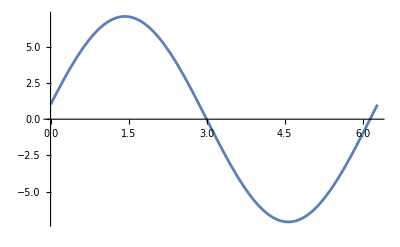

```mathematica
Plot[Cos[t]+ell*Sin[t],{t,0,2*Pi}]
```

```mathematica
Sqrt[1+ell^2]
```

7.07107

```mathematica
mat={{m00,m01},{m01,m11}}
```

{{m00,m01},{m01,m11}}

```mathematica
k={k0,k1}
```

{k0,k1}

```mathematica
p=Inverse[mat-t*IdentityMatrix[2]].mat.k
```

{k0 (-m01^2/(-m01^2+m00 m11-m00 t-m11 t+t^2)+(m00 (m11-t))/(-m01^2+m00 m11-m00 t-m11 t+t^2))+k1 (-(m01 m11)/(-m01^2+m00 m11-m00 t-m11 t+t^2)+(m01 (m11-t))/(-m01^2+m00 m11-m00 t-m11 t+t^2)),k0 (-(m00 m01)/(-m01^2+m00 m11-m00 t-m11 t+t^2)+(m01 (m00-t))/(-m01^2+m00 m11-m00 t-m11 t+t^2))+k1 (-m01^2/(-m01^2+m00 m11-m00 t-m11 t+t^2)+(m11 (m00-t))/(-m01^2+m00 m11-m00 t-m11 t+t^2))}

```mathematica
Solve[Dot[p,p]==1&&Dot[p-k,mat.(p-k)]==1,t]
```

{}